# Determinant and compound matrix methods -- an example

Prepared by Yibin Fu (y.fu@keele.ac.uk) for the advanced summer schools 2022 in CISM

We consider the eigenvalue problem
ϵ^4 (d^4 w)/dx^4+2  ϵ^2 λ d/dx(sin(x) dw/dx)+w=0,      w=(d^2 w)/dx^2=0    for x=0, π
We would like to find the minimum value of λ, as a function of the mode number 1/ϵ, at which w has a non-trivial solution

## Determinant method

```mathematica
temp=Derivative[4][w][x]/.Solve[ϵ^4 Derivative[4][w][x]+2 ϵ^2 λ D[Sin[x] w'[x],x]+w[x]==0,Derivative[4][w][x]][[1]]
```

(-w[x]-2 ϵ^2 λ Cos[x] w'[x]-2 ϵ^2 λ Sin[x] w''[x])/ϵ^4

```mathematica
(*y[1]=w[x], y[2]=w'[x], y[3]=w''[x],y[4]=w'''[x]*)
```

```mathematica
a41=Coefficient[temp,w[x]]; a42=Coefficient[temp,w'[x]]; a43=Coefficient[temp,w''[x]]; a44=Coefficient[temp,Derivative[3][w][x]];
```

```mathematica
matrixA={{0,1,0,0},{0,0,1,0},{0,0,0,1},{a41,a42,a43,a44}};
```

```mathematica
MatrixForm[matrixA]
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1/ϵ^4 | -(2 λ Cos[x])/ϵ^2 | -(2 λ Sin[x])/ϵ^2 | 0)

We use the notation yy={y[1],y[2],y[3],y[4]};
The bcs at x=0 are w=y[1]=0, w’’=y[3]=0. Two independent solutions are yy=[0,1,0,0] and yy=[0,0,0,1];
Using each as initial condition to integrate from x=0 to Pi/2, we obtain two independent solutions, yy^(1) and yy^(2), say. A genera solutions is given by y=c_1 yy^(1)+c_2yy^(2)=[yy^(1), yy^(2)] c
The bcs at x=Pi/2 are w’=y[2]=0, w’’’=y[4]=0, which may be written in the matrix form
(0 | 1
0 | 00
00
1) yy=0. On substituting the general solution into this bc, we obtain
(0 | 1
0 | 00
00
1) [yy^(1), yy^(2)] c=0. It then follows that det[(0 | 1
0 | 00
00
1) [yy^(1), yy^(2)] ]=0

```mathematica
ϵ=0.1;
```

```mathematica
MB={{0,1,0,0},{0,0,0,1}};
err[λ0_]:=Module[{},λ=λ0;  AA0=matrixA;
sol1=NDSolve[{yy'[x]-AA0.yy[x]==0,yy[0]=={0,1,0,0}},yy,{x,0,Pi/2}];
yyr1=yy[Pi/2]/.sol1;
sol2=NDSolve[{yy'[x]-AA0.yy[x]==0,yy[0]=={0,0,0,1}},yy,{x,0,Pi/2}];
yyr2=yy[Pi/2]/.sol2;bbcc=MB.Transpose[Join[yyr1,yyr2]];
N1=Det[bbcc]
]
```

Let’s  find out where roughly the first root is

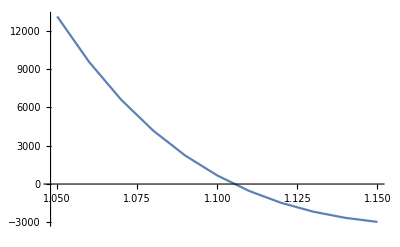

```mathematica
data=Table[{t,err[t]},{t,1.05,1.15,0.01}]; ListPlot[data,Joined->True]
```

```mathematica
froot[s0_, s1_]:=Module[{u0,u1, v0,v1},u0=s0; u1=s1; v0=err[u0]; v1=err[u1];Do[u2=(u1 v0-u0 v1)/(v0-v1);u0=u1;v0=v1;u1=u2;v1=err[u1];If[k==100, Print["No solution found"]];If[Abs[1-v1/v0]<10^(-7), Break[]],{k,1,100}]; u1];
```

```mathematica
froot[1.1,1.12]
```

1.10517

```mathematica
u0=1.1; u1=1.12; v0=err[u0]; v1=err[u1];
```

```mathematica
u0=u1;v0=v1;u1=u2;v1=err[u1]
```

-0.0000308004

```mathematica
ClearAll;
```

## The compound matrix method

```mathematica
ClearAll["`*"];
```

### Integrate from left and right, respectively

```mathematica
ϵ=0.1; en=1/ϵ;    (* e = ϵ, λ = λ, gamma=γ *)
a42[x_,λ_]:=-2 en^2 λ Cos[x]; a43[x_,λ_]:=-2 en^2 (λ Sin[x]);  (*from (A22) *)
left[x0_,λ_]:=Module[{λ0}, λ0=λ; {z1[x0],z2[x0],z3[x0],z4[x0],z5[x0],z6[x0]}/.NDSolve[{z1'[x]-z2[x]==0,z1[0]==0, z2'[x]-z3[x]-z4[x]==0,z2[0]==0,z3'[x]-a42[x,λ0]*z1[x]-a43[x, λ0]*z2[x]-z5[x]==0,z3[0]==0,z4'[x]-z5[x]==0,z4[0]==0,z5'[x]-en^4 z1[x]-a43[x,λ0]*z4[x]-z6[x]==0,z5[0]==1, z6'[x]-en^4 z2[x]+a42[x,λ0]*z4[x]==0,z6[0]==0},{z1,z2,z3,z4,z5,z6},{x,0, Pi/2}]];

right[x0_,λ_]:=Module[{λ0}, λ0=λ; {z1[x0],z2[x0],z3[x0],z4[x0],z5[x0],z6[x0]}/.NDSolve[{z1'[x]-z2[x]==0,z1[Pi/2]==0, z2'[x]-z3[x]-z4[x]==0,z2[Pi/2]==1,z3'[x]-a42[x,λ0]*z1[x]-a43[x, λ0]*z2[x]-z5[x]==0,z3[Pi/2]==0,z4'[x]-z5[x]==0,z4[Pi/2]==0,z5'[x]-en^4 z1[x]-a43[x,λ0]*z4[x]-z6[x]==0,z5[Pi/2]==0, z6'[x]-en^4 z2[x]+a42[x,λ0]*z4[x]==0,z6[Pi/2]==0},{z1,z2,z3,z4,z5,z6},{x,Pi/2, 0}]]
```

### Defines the error function N(x, λ)

```mathematica
nfunction[x0_,λ_]:=Module[{a,b}, a=left[x0,λ]; b=right[x0,λ];a[[1,1]]*b[[1,6]]-a[[1,2]]*b[[1,5]]+a[[1,3]]*b[[1,4]]+a[[1,4]]*b[[1,3]]-a[[1,5]]*b[[1,2]]+a[[1,6]]*b[[1,1]]];   (*from (A19) *)
```

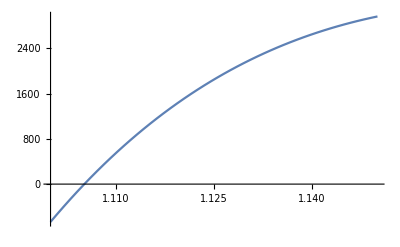

```mathematica
Plot[nfunction[Pi/4,λ],{λ,1.1,1.15}]
```

```mathematica
err[s_]:=nfunction[Pi/4,s]  (*left and right solutions are matched at x=Pi/4 *)
```

```mathematica
froot[s0_, s1_]:=Module[{u0,u1, v0,v1},u0=s0; u1=s1; v0=err[u0]; v1=err[u1];Do[u2=(u1 v0-u0 v1)/(v0-v1);u0=u1;v0=v1;u1=u2;v1=err[u1];If[k==100, Print["No solution found"]];If[Abs[1-v1/v0]<10^(-7), Break[]],{k,1,100}]; u1];
```

```mathematica
froot[1.1,1.2]
```

1.10517